0.43

-0.522817

0.130704

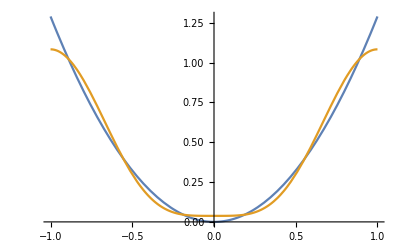

```mathematica
p=1.290;
s[t_]:=p t^2;
T=2;
ω0=2 π/T;
a0=1/T Integrate[s[t],{t,-1,1}]
a1=2/T Integrate[s[t]Cos[ω0 t],{t,-1,1}]
a2=2/T Integrate[s[t]Cos[2ω0 t],{t,-1,1}]
f[t_]:= a0+a1 Cos[ω0 t]+a2 Cos[2ω0 t]
Plot[{s[t],f[t]},{t,-1,1}]
```

```mathematica
w[t_]:= a t^2 + b t +c
Integrate[(f[t]-w[t]) t^2,{t,-1,1}]
Integrate[(f[t]-w[t]) t,{t,-1,1}]
Integrate[(f[t]-w[t]),{t,-1,1}]
```

0.5118-0.4 a-0.666667 c

0.-0.666667 b

-0.666667 (-1.29+a+3. c)

```mathematica
eq1=0.5117996575118942-0.4 a-0.6666666666666666 c ==0;
eq2 = 0.-0.6666666666666666 b ==0;
eq3 = -0.6666666666666666 (-1.29+a+3. c) ==0;
Solve[{eq1,eq2,eq3},{a,b,c}]
```

{{a→1.26637,b→0.,c→0.00787564}}